Definition of the Potential

```mathematica
r[x_]:= x+ r0
r0 = 1/(4 OverTilde[a]);
Veff[x_] := 1/(8r[x]^2) -OverTilde[a]/r[x] + 2OverTilde[a]^2
```

First Coefficients

```mathematica
phiminusone[x_]:= Assuming[x>=0&&OverTilde[a]>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
Eminustwo = -2OverTilde[a]^2;
Es = {Eminustwo};
phis = {phiminusone[x]};
Eminusone = -1/2(D[phis[[1]],x] /. x-> 0)-1/(2 r[0]^2);
AppendTo[Es,Eminusone];
phizero[s_] :=Simplify[( Es[[2]] + 1/(2r[s]^2) +1/2(D[phis[[1]],x] /.x->s))/(-phiminusone[s])]
AppendTo[phis,phizero[x]];

Ezero = 3/(8 r[0]^2)-1/2(D[phis[[2]],x]/. x->0)-1/2( phis[[2]]^2 /. x->0) +(9b)OverTilde[a];
phione[s_] := Simplify[(-3/(8 r[s]^2)+1/2(D[phis[[2]],x]/. x->s)+1/2( phis[[2]]^2 /. x->s) -(9b)OverTilde[a]+ Ezero)/(-phiminusone[s])]
```

Recursion Relation

```mathematica
Energy[n_]:= Energy[n] = Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,EvenQ[n],Simplify[-1/2(D[phi[n],x]/.x->0)-1/2Sum[(phi[m]/.x->0)(phi[n-m]/. x->0),{m,0,n}]+(-1)^(n/2)(9b)^(n/2+1)/Factorial[n/2+1]OverTilde[a]r[0]^(n/2)],True,Simplify[-1/2(D[phi[n],x]/.x->0)-1/2Sum[(phi[m]/.x->0)(phi[n-m]/. x->0),{m,0,n}]]]
phi[n_]:= phi[n] = Which[n==-1,phiminusone[x],n==0,phizero[x],n==1,phione[s],OddQ[n],Simplify[(Energy[n-1]+ 1/2 D[phi[n-1],x]+1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]+(-1)^((n+1)/2)(9b)^((n+1)/2)/Factorial[(n+1)/2]OverTilde[a]r[x]^((n-1)/2))/(-phiminusone[x])],True,Simplify[(Energy[n-1]+ 1/2 D[phi[n-1],x]+1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}])/(-phiminusone[x])]]
```

```mathematica
Clear[Energy,phi]
```

Redefinitions

```mathematica
OverTilde[a] = 1/k^2;
maxkOrder = 100;
k=3
```

3

```mathematica
(*maxkOrder = 170;
ProgressIndicator[Dynamic[n],{100,150}]
times = Table[Timing[Energy[n]][[1]],{n,-2,maxkOrder}];*)
```

```mathematica
Energy[10]
```

-(1299078 b^6+531441 b^5 ã-262440 b^4 (ã)^2+266240 (ã)^6)/(10240 (ã)^4)

```mathematica
perturbationorder = 50;
EnergySeries = Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder}],k],b]],b]+O[b]^(perturbationorder+1)];
EnergySeriesplusOne= Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder+1}],k],b]],b]+O[b]^(perturbationorder+1)];
Coefficients = {-2/(k-1)^2};
Do[AppendTo[Coefficients,Collect[Coefficient[EnergySeries, b,n],k] ],{n,1,perturbationorder}]
Coefficientstwo = {-2/(k-1)^2};
Do[AppendTo[Coefficientstwo,Collect[Coefficient[EnergySeriesplusOne, b,n],k] ],{n,1,perturbationorder}]
(*Table[Length[Coefficients[[(n+1)]] /. Sum ->List]==2(n-1),{n,2,perturbationorder}]*)
```

```mathematica
Table[Coefficients[[n]] -Coefficientstwo[[n]],{n,1,perturbationorder+1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

0

```mathematica
k=3
```

3

```mathematica
k=3
PertrubativeFactors = {1};
Do[AppendTo[PertrubativeFactors,b^n],{n,1,perturbationorder}]
RelativeError = Coefficients*PertrubativeFactors;
ListPlot[Abs[RelativeError /. b->0.5]]
```

3

-Graphics-

```mathematica
ListPlot[Abs[Coefficients]]
```

-Graphics-

```mathematica
PartialSums = Table[Total[Take[Coefficients,order+1]*Table[b^n,{n,0,order}]],{order,0,perturbationorder}];
PadeNN = Table[PadeApproximant[PartialSums[[n]],{b,0,Floor[n/2]}] ,{n,3,perturbationorder}];
PadeNNplusone = Table[PadeApproximant[PartialSums[[n]],{b,0,{Floor[n/2],Floor[n/2]+1}}] ,{n,3,perturbationorder}];
```

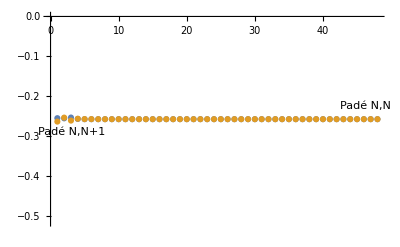

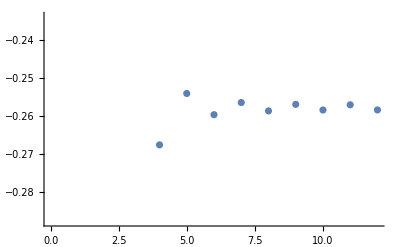

-0.258319

-0.257639

```mathematica
value = 0.3;
PadeAproximationsnn = Table[(PadeNN[[n-2]] /. b->value),{n,3,perturbationorder}];
PadeAproximationsnplusone = Table[(PadeNNplusone[[n-2]] /. b->value),{n,3,perturbationorder}];
ListPlot[{Labeled[PadeAproximationsnn,"Padé N,N",Right],Labeled[PadeAproximationsnplusone,"Padé N,N+1",Left]}]
bestindex =Position[Abs[RelativeError /. b->value],Min[Abs[RelativeError /. b->value]]][[1,1]];
ListPlot[Table[PartialSums[[s]],{s,0,bestindex}] /. b-> value]
BestasymAprox = PartialSums[[bestindex]] /. b->value
BestEstimatePade= N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->value]
```

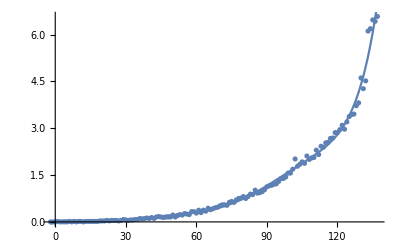

```mathematica
ns = Table[n,{n,-2,maxkOrder}];
data = Table[{ns[[n]],times[[n]]},{n,1,maxkOrder}];
model = Fit[data,Table[x^(n),{n,0,7}],x];

Show[ListPlot[data],Plot[model,{x,-2,maxkOrder*10}]]
```

```mathematica
phissprime = Simplify[Collect[Collect[Sum[k^(-n)phi[n],{n,-1,maxkOrder}],k],b]];
```

```mathematica
phiss = Normal[Collect[Integrate[phissprime,x],b]+O[b]^(26)];
```

```mathematica
phisssos[s_] := PadeApproximant[phiss/. x->s ,{b,0,12}]
```

```mathematica
us[r_] := Exp[phisssos[r -r0]];
```

ⅇ^(((b^8 (197330784058236088638841792571894540712660527944536515903851748803530729548633195505620898048666189740352562337610264260307287639511404077436753336962226605252182474693011205343-16634214152484403875831604621617965435574593218086657449334003806605283933225582321223486545641713712951449557451553175995230736318731270017084689712335919558002405989084031242 Log[4]))/4095883156187880212434502603923832861682200210677761644561933561694895085712811111042312966940324495979474902341919955243840496210294007934843655597511350196437200576027033600+(b^7 (-2910053885168174990273142385979711711893399299474626404728954632992939373679533502919165363080969074639491273112272839727618656425563208928106392117411319652444326060893323-2031680947055329351703172907700944048687750685753788681655015413213149070729336772473908891870712146090800046982031826127230677249903317583657609737565752399926287852338503 Log[4]))/59257568810588544740082502950286933762763313233185208978037233242113644179872845935218648248557935416369717915826388241375007178968373957390677887695476710017899313889280+(-5474401089420219382077155933569751762+5474401089420219382077155933569751763 Log[4])/5474401089420219382077155933569751763+(10604697395295608719372460182054989880338401955168606659333071339821165593850236750599701627194285141506938996820400395693 b (-5474401089420219382077155933569751762+5474401089420219382077155933569751763 Log[4]))/3342196497539348285073282440966966751884718728708254703785323114050729261835439745059254555490502786623535325037644076227068042414911482769063240722826007949+(b^2 (-225750114251934169185596826458154131065391887114434365695596672191730475552104462278812445280087240210576654103379353002094790175965879520872891091717117087780953+223794929300873650438828956230188455556419584725707978034126443409577780841833753130667837535196059571744595568743788169827966285500919218211004302965734616185062 Log[4]))/1925105182582664612202210685996972849085597987735954709380346113693220054817213293154130623962529605095156347221682987906791192430989014074980426656347780578624+(b^3 (-2522622949456787288669048283206286003508694224728466495848931802117752312113770753481155819125657695037632923984857387669634904113804001483249291184950610075628263+2417466057089494034810473605978943902244033807236019781610427303371892849040378343799313818875318548552937368850427994833570350020202215327160452013931889584522962 Log[4]))/6417017275275548707340702286656576163618659959119849031267820378977400182724044310513768746541765350317187824072276626355970641436630046916601422187825935262080+(35 b^4 (-92692466578393100176316358430631642102434632231710833159335438257289211181581666082687190104365899494705714150455115512126024364665754510482069270899495487024765373+79702169284730013192655771518351840798216854179032155882368625258307203408750941441665466571529520243848854422674163136994283396634951414002184644862024216050292406 Log[4]))/4627097256625355654573135728831835185713295074522685808146183014601304025089550884167794850839715601935380233677716266044411897185239372496664065492235021052977152+(b^5 (-28363309857341181014917509017971656429700124881733950878362558178316978642986260520871033749315055506063486279415373060731079835585684634037047757607895020585083068939+17237877708557352295844531200874452867642476922492592869869250241814770185934750305758961604621441815445330803887343917155480092193031687126935836668107302300569408126 Log[4]))/41643875309628200891158221559486516671419655670704172273315647131411736225805957957510153657557440417418422103099446394399707074667154352469976589430115189476794368+(b^6 (-216868435270104866088777821263490808763777171520561582622473866950489714400532767987473568548686290014552188918079428606256085566538311047661713689182147187672291714428668+29727729911855989923647736768754138164667472774984317122926191000546726452309337348570403559563668056920284650769919937828905580653861745570231208897601052547645834236627 Log[4]))/604669069495801476939617377043744222069013400338624581408543196348098409998702509543047431107734034860915488937003961646683746724167081197864060078525272551203054223360)/(1+(10604697395295608719372460182054989880338401955168606659333071339821165593850236750599701627194285141506938996820400395693 b)/610513632988720644956945113829640391731705319764612143005239510570819297294700359303797998310409226274925887245681889823+(20440129033783970670122092619783490953951511551357528085035381745671354815255728476163005457173881457379007603535735371527137 b^2)/175827926300751545747600192782936432818731132092208297185508979044395957620873703479493823513397857167178655526756384269024+(220797308929507212561965858921740216126340513811629415110327159857549138985174450297727847946507871106369108783925029851048787 b^3)/586093087669171819158667309276454776062437106974027657285029930147986525402912344931646078377992857223928851755854614230080+(254783663034542808857706280205782808713710669052929570937424369237510395202727576499024769922131112622389900904675141092805665835 b^4)/422612189081984159734676374475608990526087983268738876079658914965374817250526661518712265582424716248934297372754900500836352+(1574407631719853975387697442262597385706977516029518521733495415359756933327023388798041068063355832713334906796069415480378752101 b^5)/3803509701737857437612087370280480914734791849418649884716930234688373355254739953668410390241822446240408676354794104507527168+(5430316380965864178307890079900048362356344594026735264276366972726114714698366562872782906148611760752969178115880173972013339158529 b^6)/110453921738467379988255017232945165763898355307117592652179654015350362236597648254530637732622523838821467961343220794898588958720-(53017696466291824377963406962212407652044882907734470815156588622373075635785880692076593583527435423923767600165657563430176063056283 b^7)/1546354904338543319835570241261232320694576974299646297130515156214905071312367075563428928256715333743500551458805091128580245422080-(217038929800943934117938908893615364841422853327633141550700861945621204651701706210579860830805379578728177021877545401505537201465926081 b^8)/53442025493940057133517307537988189003204580231795776028830603798787119264555406131472103760552081934175379058416303949403733281787084800))

```mathematica
us[1] /. b->0.1
```

General::munfl: (1.×10^-12)/(946769542757930108818900684500217913789852426108599280870443285578930«254»4520836432245633220673790397063575543637258362973014824407972928552960) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.01/(137741368801443192856453256807330727858868448826728696473874479462437«229»5561369878490586037825003578274570504859227229535021360242576328954816) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.001/(520662374069455268997393310731710151306522736565034472671245532368015«231»2197814069441522297851352587787650836787892764238074171693852344920448) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.09758

4 ⅇ^(-4638397686588101979328150167890591454318967698008/4638397686588101979328150167890591454318967698009-(65 b^2)/64+(1445 b^3)/1152-(146075 b^4)/73728+(49817 b^5)/12288-(34807145 b^6)/3538944+(9274524703 b^7)/346816512-(7025632798049 b^8)/88785027072+(600558252490871 b^9)/2397195730944-(80479213375710203 b^10)/95887829237760+(4568012967345947209 b^11)/1546990311702528-(48338810872750071856387 b^12)/4455332097703280640+(3902442232402052047790023 b^13)/94118890563981803520-(2770854240456660543985288355 b^14)/16866105189065539190784+(113546068874723080381929281533 b^15)/168661051890655391907840-(2459002496564090765318975234253727 b^16)/863544585680155606568140800+(3097639825982815762874563353994897621 b^17)/249564385261564970298192691200-(1500735806527357956503493206245905492901 b^18)/26952953608249016792204810649600+(333107096098207311024956346809387741639903 b^19)/1297335500343719341598124885934080-(148473936207569103987843606925681605209302129 b^20)/122102164738232408620999989264384000+(2341599278120174505349879153463461782878177797 b^21)/396277025559536089797245419703500800-(307311752412361320239004146256829909530900709781 b^22)/10437990768479753331258056225115340800+(174287251495420670575068629501728105501773700310670211 b^23)/1159556394470415797569457466048063209472000-(376774043956994481925433089329045644921729520652197606973 b^24)/479521167436381179056415641344183678009344000+(655081663214956099188839882776098499927850818312327073592721 b^25)/155844379416823883193335083436859695353036800000-(2982221917556526227840539806014438061986083769553733501159127 b^26)/129662523674797470816854789419467266533726617600+(2026738902978952993214914563829531222984028767472842708678730268523 b^27)/15753996626487892704247856914465272883847784038400000-(305245281520916912047693611596070117488074945687015376096989458327701 b^28)/415164146392151525382531758687084838350812191129600000+(1306195268437972076465651425946202781551391614371581619840568181490431489 b^29)/304389835947107197866361874561500099174439071619481600000-(36387166542784686869635237198051972039564172920983199260917417609122200063089 b^30)/1424544432232461686014573572947820464136374855179173888000000+(1542597520216032652934098900084967511877513388420308588756685612396318786369667089 b^31)/10951897595003165442080041628822843728280449886617488850944000000+(11553800049050259892147808566848971690956331505374507015828974472151264728298977172013 b^32)/5607371568641620706344981313957295988879590341948154291683328000000-(19781664220033948411918493186451048010191751651492139689583180615668460512271361189210179 b^33)/61681087255057827769794794453530255877675493761429697208516608000000+(1421728142237919653819972424726654187217493741521457698273874453760259663598931573060360919 b^34)/121574316908519776473798435444639344918316915239919403193597952000000+(21368746160065556277992787650086590051955877940035181570185620405711048937730794488911900027689 b^35)/73400493833518815046055805399701004494433837576101339678134763520000000-(1030843249326121582277633329755610835676251467483245889266324646805173607886094932221263760630612101 b^36)/56371579264142449955370858546970371451725187258445828872807498383360000000-(79252018044327549590164265281572680978177533596419308801235016438778832093778709905566472750320031631759 b^37)/1852144608302664335733664928419258524417882752563496153444963166883676160000000+(94340252034548904485194612248491812421631452496692419234151222039976624585545599304786277677920052036531 b^38)/25226342335305105647985400458756926139024926379001022878461863921713152000000+(13097590715130373080106609664942597910545419237001973483688932722882078072004839078848676913422179925862455707 b^39)/430569146588948791459967282183112334617616037537113929318499672677899304960000000+(121923351988927654827808210035403250134620868845249638422578587498591106101311553841641153049109807175506214887 b^40)/4345632945164900603974437875836977922671301009651019991637547716823325081600000000-(16115507931503472059359493582666069569502363540099060484159908495678330166640415913063718516366073169755202458446933 b^41)/21874443559239803757424862263016535442431312897241075125572915815317917222830080000000-(1138780190184301820200087465786035217682039052076479500546529225092571873276373512255941537091339842255935084581788943943 b^42)/211674615434051732999848907146758410169319328644022435775143991761668421381882118144000000-(1726466221945516891621177691316250190293714708388327475891070799729470348829782608803502411664946659306470226110531326427149 b^43)/80864951226768936842297650684784359587411454269173033832281248092422502300640503398400000000-(85491423357830663593316800337008941878347711531758194519816220057321664595437681754694995188648769135192861225004417229405915921 b^44)/1722100001325271278993570768983167721773514330116308928492261459376229608994440160372326400000000-(3647336430600073366267758191047597309025515012572719461032926458833133481622872819051921532651660940234934490876122650081388039 b^45)/1037872768655855458322018097378248403747430511454025470296675433106209808992184918081536000000000+(141664402153701923133185375692724139259928592066405138096552726736935930854496580914675757881985413072531446940704884702767354669214613 b^46)/342215712263357908561602383212335089670832767680712910269982197207244347899375148669188702208000000000+(111035271987844289823304024641407650436556087470498545327314672857344871342243794411329110506120534305602534688004495215231182069134109383 b^47)/125992418064959603335429944086008035513811597301115803131065112271800460751619950568372973862912000000000-(25525446631087925238497913913398560922056008691023735448176353929476705864949934338049421310335928344210872916219195898359280066258792064031 b^48)/19352435414777795072322039411610834254921461345451387360931601244948550771448824407302088785343283200000000+(42605139883740577245503145718816752283622654736277137586931430581514691244705246969450974127751977828083621463495273303684083258901319381391859 b^49)/88505137963583782797419460242433548659174149886531011530660523026898038861425956956061552711636615168000000000-(39550020996796605518175688007571482585802445508083771512060763940535133363168207249648446698012799313941154173053453135548296323273604102314209 b^50)/722490922151704349366689471366804478850401223563518461474779779811412562134089444539277981319482572800000000000)

```mathematica
Clear[r]
```

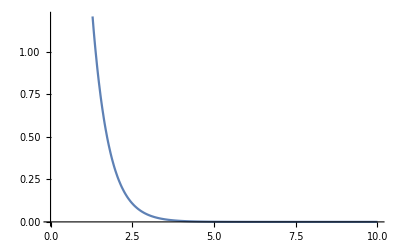

```mathematica
Show[Plot[ (1/r us[r]  /. b->0.1)^2 ,{r,0,10}]]
```

General::munfl: 129.676/(255908909076365734781332123245049072367533904869833726566735296227267«310»2164341951108150752528169302924991750576512593629164962149841240064000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 656.364/(302292398846457024210448570583214216734149425127491089506956068668459«312»4412892974650307642389998908014650536850550122445111153949996482560000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 25.6196/(114366307614710121124554884417652230542442949497719111364386479516124«308»5886439157370462659080624185477571048547350483631659303780346757120000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

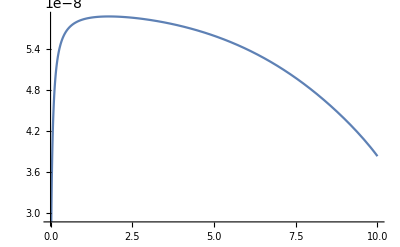

```mathematica
Plot[Cs u ,{r,0,10}]
```

```mathematica
L = NIntegrate[(1/r us[r]  /. b->0.1)^2,{r,0,10}]
Cs =Sqrt[1/L]
```

$Aborted

6.17729×10^-8

```mathematica
PadeApproximant[phiss,{b,0,2}]
```

(-(b (459+156 x+16 x^2) (1195740+531440 x-531441 Log[9+4 x]))/(19131876 (9+2 x))+(-1195740-531440 x+531441 Log[9+4 x])/531441+1/(5509980288 (9+2 x)^2)b^2 (408824701740+809708243184 x+381953466576 x^2+65794537728 x^3+3035595648 x^4-170060800 x^5-181700209341 Log[9+4 x]-55960737300 x Log[9+4 x]+3883770828 x^2 Log[9+4 x]+2091751776 x^3 Log[9+4 x]+170061120 x^4 Log[9+4 x]))/(1+(b (459+156 x+16 x^2))/(36 (9+2 x))+(b^2 (-341901-105300 x+7308 x^2+3936 x^3+320 x^4))/(10368 (9+2 x)^2))

```mathematica
Clear[x]
Clear[r]
```

```mathematica
EnergySeries = Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,10}],k],b]],b]+O[b]^(5+1)];
```

```mathematica
EnergySeries
```

-(81 b^2 (-1+k))/(8 k^3)+(59049 b^5 (-9-16 k+7 k^2))/(10240 k^10 (ã)^3)-(2187 b^4 (-6+8 k+2 k^2-9 k^3+4 k^4))/(512 k^10 (ã)^2)+(243 b^3 (-1+k)^2 (1+k))/(32 k^7 ã)+9 b ã-(2 (13+12 k+11 k^2+10 k^3+9 k^4+8 k^5+7 k^6+6 k^7+5 k^8+4 k^9+3 k^10+2 k^11+k^12) (ã)^2)/k^10

```mathematica
OverTilde[a] = a/k^2
```

a/k^2

```mathematica
EnergySeries
```

-(81 b^2 (-1+k))/(8 k^3)+(9 a b)/k^2+(243 b^3 (-1+k)^2 (1+k))/(32 a k^5)+(59049 b^5 (-9-16 k+7 k^2))/(10240 a^3 k^4)-(2187 b^4 (-6+8 k+2 k^2-9 k^3+4 k^4))/(512 a^2 k^6)-(2 a^2 (13+12 k+11 k^2+10 k^3+9 k^4+8 k^5+7 k^6+6 k^7+5 k^8+4 k^9+3 k^10+2 k^11+k^12))/k^14

```mathematica
b = g*a
```

a g

```mathematica
Simplify[EnergySeries/a^2]
```

-762939446/6103515625+(9 g)/25-(81 g^2)/250+(729 g^3)/3125-(3190833 g^4)/8000000+(2539107 g^5)/3200000

```mathematica
k=5
```

5